# Hermite Gauss mode plots

Ruvi Lecamwasam, September 2023
Plot the Hermite Gauss modes

## Hermite-Gauss modes

```mathematica
(* Optimum displacement when restricted to |θ|<3 *)
θopt3=-1.0787266067642645;
(* Optimum displacement when restricted to |θ|<5 *)
θopt5=-4.645893701554011;

σPrior = 0.25; (* Variance of the prior distribution *)
(* Continuous Gaussian as prior distribution *)
ψPhoton[ϕ_]:=1/(2π)^(1/4)Exp[-(x-ϕ)^2/4];
```

### Make plots

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
labelStyle=Directive[FontSize->25,FontColor->Black,FontFamily->"Times New Roman",FontSlant->Plain];
ticksStyle=Directive[FontSize->25,FontColor->Black,FontFamily->"Times New Roman",FontSlant->Plain];
axesStyle=Directive[Black];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle,AxesStyle->axesStyle,TicksStyle->ticksStyle,AspectRatio->1/1.8];

hgModesPlot=Module[{ϕqList,colorList,fontStyle,hgPlot,ψPlot,xRange},
xRange=10;
colorList={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.880722, 0.611041, 0.142051]};
fontStyle=Sequence[FontSize->30];
ϕqList={
Callout[ψHGq[x,0]^2,Style["h_0^2",FontColor->colorList[[0+1]],Evaluate@fontStyle],{-1.4,Above}],
Callout[ψHGq[x,1]^2,Style["h_1^2",FontColor->colorList[[1+1]],Evaluate@fontStyle],{3.2,Above}],
Callout[ψHGq[x,2]^2,Style["h_2^2",FontColor->colorList[[2+1]],Evaluate@fontStyle],{-5,Above}],
Callout[ψHGq[x,3]^2,Style["h_3^2",FontColor->colorList[[3+1]],Evaluate@fontStyle],6]
(*,Callout[ψHGq[x,4]^2,Style["h_4^2",FontColor->colorList[[4+1]],Evaluate@fontStyle],-7.3]*)};

hgPlot=Plot[Evaluate@ϕqList,{x,-xRange,xRange},Evaluate@plotOpts,AxesLabel->{"x",None},PlotStyle->({Thick,#}&/@colorList),PlotRange->{{-xRange,xRange},{0,0.24}},PlotRangePadding->None,Ticks->{Automatic,None}
,Epilog->{Text[Style["θ=0",FontColor->Gray,FontSize->25,FontFamily->"Times New Roman"],{-0.05,0.225}]},PlotLabel->Style["HG modes and point source wavefunctions",labelStyle]];
ψPlot=Plot[1/3{ψPhoton[-1],ψPhoton[1]},{x,-xRange,xRange},PlotStyle->{{Gray,Dashed,Thickness[0.005],Opacity[1]}}];
Show[hgPlot,ψPlot,AspectRatio->0.4,Axes->{True,False}]
]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
Export["fig_HGModes.png",hgModesPlot,ImageResolution->300];
```

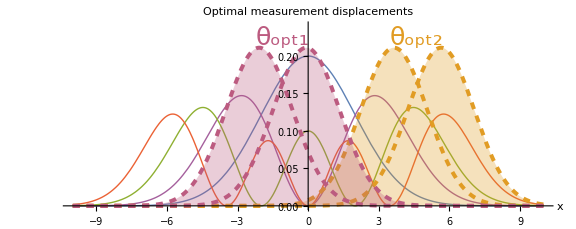

```mathematica
hgModesOptimalPlot=Module[{ϕqList,colorList,fontStyle,hgPlot,ψPlot5,ψPlot5Shade,ψPlot3,ψPlot3Shade,xRange,θ3Colour,θ5Colour},
xRange=10;
colorList={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.880722, 0.611041, 0.142051]};
fontStyle=Sequence[FontSize->30];
ϕqList={
Callout[ψHGq[x,0]^2,Style["h_0^2",FontColor->colorList[[0+1]],Evaluate@fontStyle],{-1,Above}]
,Callout[ψHGq[x,1]^2,Style["h_1^2",FontColor->colorList[[1+1]],Evaluate@fontStyle],{-3.4,Above}]
,Callout[ψHGq[x,2]^2,Style["h_2^2",FontColor->colorList[[2+1]],Evaluate@fontStyle],{-5.05,Above}]
,Callout[ψHGq[x,3]^2,Style["h_3^2",FontColor->colorList[[3+1]],Evaluate@fontStyle],-6.4](*
,Callout[ψHGq[x,4]^2,Style["h_4^2",FontColor->colorList[[4+1]],Evaluate@fontStyle],-7.5]*)
}/.Callout[Y_,_,_]->Y;

θ3Colour=RGBColor[0.736782672705901, 0.358, 0.5030266573755369];
θ5Colour=RGBColor[0.880722, 0.611041, 0.142051];

hgPlot=Plot[Evaluate@ϕqList,{x,-xRange,xRange},Evaluate@plotOpts,AxesLabel->{"x",None}
,PlotStyle->({Opacity[1],Thick,#}&/@colorList)
,PlotRange->{{-xRange,xRange},{0,0.24}},PlotRangePadding->None,Ticks->{Automatic,None}
,Epilog->{Text[Style["θ_opt2",FontColor->θ5Colour,FontSize->25,FontFamily->"Times New Roman"],{4.6,0.225}],Text[Style["θ_opt1",FontColor->θ3Colour,FontSize->25,FontFamily->"Times New Roman"],{-1.1,0.225}]},
PlotLabel->Style["Optimal measurement displacements",labelStyle]
];
ψPlot5=Plot[
{
1/3 ψPhoton[-1-θopt5],
Callout[1/3 ψPhoton[1-θopt5],Style["θ_opt5",FontColor->θ5Colour,FontSize->20],{7,Above}]/.Callout[Y_,_,_]->Y
}
,{x,-xRange,xRange}
,PlotStyle->{{θ5Colour,Thickness[0.005],Dashed}}];
ψPlot5Shade=Plot[1/3 Max[ψPhoton[-1-θopt5],ψPhoton[1-θopt5]],{x,-xRange,xRange},PlotStyle->None,FillingStyle->{Directive[θ5Colour,Opacity[0.3]]},Filling->Axis,Exclusions->None];
ψPlot3=Plot[{Callout[1/3 ψPhoton[-1+θopt3],Style["θ_opt3",FontColor->θ3Colour,FontSize->20],{-3.3,Above}]/.Callout[Y_,_,_]->Y,1/3 ψPhoton[1+θopt3]},{x,-xRange,xRange},PlotStyle->{{θ3Colour,Thickness[0.005],Dashed}}];
ψPlot3Shade=Plot[1/3 Max[ψPhoton[-1+θopt3],ψPhoton[1+θopt3]],{x,-xRange,xRange},PlotStyle->None,FillingStyle->{Directive[θ3Colour,Opacity[0.3]]},Filling->Axis,Exclusions->None];


Show[hgPlot,ψPlot5,ψPlot5Shade,ψPlot3,ψPlot3Shade,AspectRatio->0.4,Axes->{True,False}]
]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["fig_HGModesOptimal.png",hgModesOptimalPlot,ImageResolution->300];
```